Inserisco la matrice A

```mathematica
A=({{-17/5, -4/5, 12/5}, {-12/5, -9/5, 12/5}, {4/5, -2/5, -19/5}})
```

{{-17/5,-4/5,12/5},{-12/5,-9/5,12/5},{4/5,-2/5,-19/5}}

```mathematica
λ=Eigenvalues[A]
```

{-5,-3,-1}

Determino gli autovettori dx di A

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{-3,2,2},{-3,2,-3},{1,1,1}}

```mathematica
MatrixForm[T]
```

(-3 | 2 | 2
-3 | 2 | -3
1 | 1 | 1)

```mathematica
λ
```

{-5,-3,-1}

Proietto lo stato iniziale lungo gli autovettori dx di A

```mathematica
Subscript[x, 0]=({{2}, {-4}, {1}})
```

{{2},{-4},{1}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{0},{-1/5},{6/5}}

```mathematica
Subscript[x, l][t_]:=∑_(i=1)^3 T[[All,i]]Exp[λ[[i]]t]Subscript[z, 0][[i,1]]
```

```mathematica
Subscript[x, l][t]
```

{-2/5 ⅇ^(-3 t)+(12 ⅇ^-t)/5,-2/5 ⅇ^(-3 t)-(18 ⅇ^-t)/5,-1/5 ⅇ^(-3 t)+(6 ⅇ^-t)/5}

Posso calcolare direttamente l’esponenziale di Matrice di A utilizzando una funzione messa a disposizione da Mathematica

```mathematica
MatrixExp[A t]
```

{{(3 ⅇ^(-5 t))/5+(2 ⅇ^-t)/5,(2 ⅇ^(-3 t))/5-(2 ⅇ^-t)/5,-6/5 ⅇ^(-5 t)+(6 ⅇ^(-3 t))/5},{(3 ⅇ^(-5 t))/5-(3 ⅇ^-t)/5,(2 ⅇ^(-3 t))/5+(3 ⅇ^-t)/5,-6/5 ⅇ^(-5 t)+(6 ⅇ^(-3 t))/5},{-1/5 ⅇ^(-5 t)+ⅇ^-t/5,ⅇ^(-3 t)/5-ⅇ^-t/5,(2 ⅇ^(-5 t))/5+(3 ⅇ^(-3 t))/5}}

```mathematica
MatrixForm[Out[17]]
```

((3 ⅇ^(-5 t))/5+(2 ⅇ^-t)/5 | (2 ⅇ^(-3 t))/5-(2 ⅇ^-t)/5 | -6/5 ⅇ^(-5 t)+(6 ⅇ^(-3 t))/5
(3 ⅇ^(-5 t))/5-(3 ⅇ^-t)/5 | (2 ⅇ^(-3 t))/5+(3 ⅇ^-t)/5 | -6/5 ⅇ^(-5 t)+(6 ⅇ^(-3 t))/5
-1/5 ⅇ^(-5 t)+ⅇ^-t/5 | ⅇ^(-3 t)/5-ⅇ^-t/5 | (2 ⅇ^(-5 t))/5+(3 ⅇ^(-3 t))/5)

```mathematica
Subscript[x, ln][t_]:=Simplify[MatrixExp[A t].Subscript[x, 0]]
```

```mathematica
Subscript[x, ln][t]
```

{{2/5 ⅇ^(-3 t) (-1+6 ⅇ^(2 t))},{-2/5 ⅇ^(-3 t) (1+9 ⅇ^(2 t))},{1/5 ⅇ^(-3 t) (-1+6 ⅇ^(2 t))}}

Grafico delle tre componenti della risposta libera

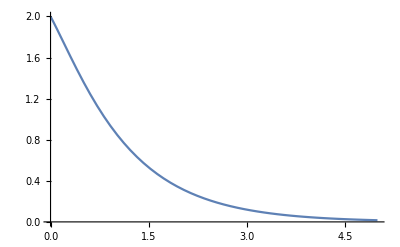

```mathematica
Plot[Subscript[x, l][t][[1]],{t,0,5}]
```

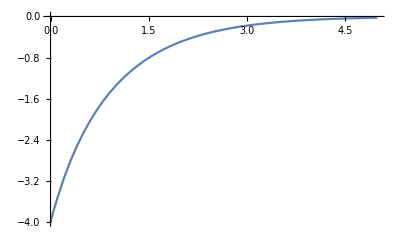

```mathematica
Plot[Subscript[x, l][t][[2]],{t,0,5}]
```

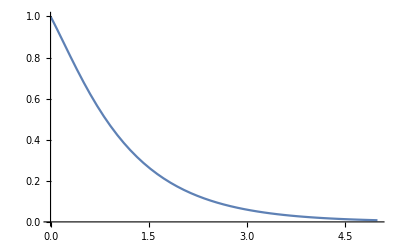

```mathematica
Plot[Subscript[x, l][t][[3]],{t,0,5}]
```

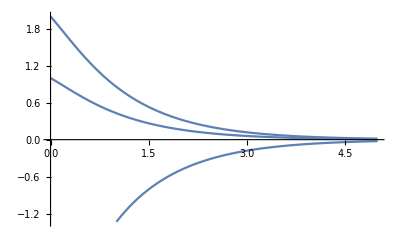

```mathematica
Plot[Subscript[x, l][t],{t,0,5}]
```

```mathematica
Limit[Subscript[x, l][t],t->∞]
```

{0,0,0}

Calcolo della dimensione dei tre sottospazi legati agli autovettori dx di A

```mathematica
NullSpace[A-(-5)IdentityMatrix[3]]
```

{{-3,-3,1}}

```mathematica
NullSpace[A-(-3)IdentityMatrix[3]]
```

{{2,2,1}}

```mathematica
NullSpace[A-(-1)IdentityMatrix[3]]
```

{{2,-3,1}}

Scelgo lo stato iniziale allineato secondo il secondo autovettore dx di A

```mathematica
Subscript[x, 0]=({{4}, {4}, {2}})
```

{{4},{4},{2}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{0},{2},{0}}

```mathematica
Subscript[x, l][t_]:=∑_(i=1)^3 T[[All,i]]Exp[λ[[i]]t]Subscript[z, 0][[i,1]]
```

```mathematica
Subscript[x, l][t]
```

{4 ⅇ^(-3 t),4 ⅇ^(-3 t),2 ⅇ^(-3 t)}